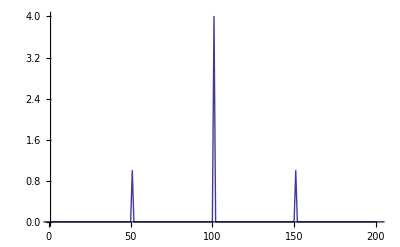

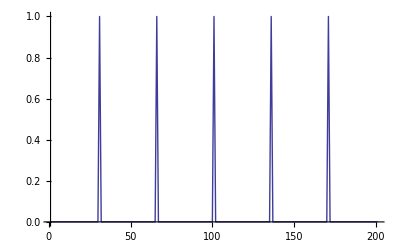

```mathematica
ΔfEOM=50;
ΔFSR=35;
imax=6;
comb=Sum[DiscreteDelta[m/ΔFSR-imax/2 +i],{i,imax}];
combnum=Table[comb,{m,-100,100}];
laser=4DiscreteDelta[m]+DiscreteDelta[m-ΔfEOM]+DiscreteDelta[m+ΔfEOM];
lasernum=Table[laser,{m,-100,100}];
ListPlot[lasernum,Joined->True,PlotRange->All]
ListPlot[combnum,Joined->True,PlotRange->All]
spectrum=DiscreteConvolve[comb,laser,m,n];
spectrumnum=Table[spectrum,{n,-100,100}];ListPlot[spectrumnum,Joined->True,PlotRange->All]
```

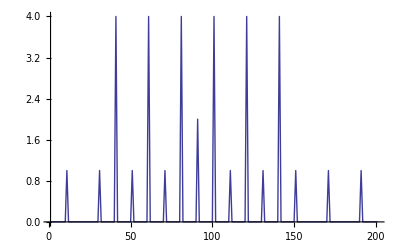

```mathematica
ΔfEOM=50;
ΔFSR=20;
```

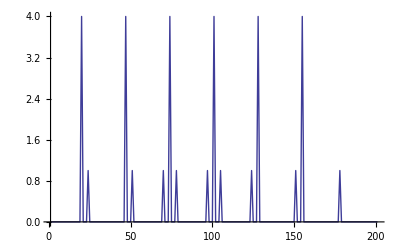

```mathematica
ΔfEOM=50;
ΔFSR=27;
```

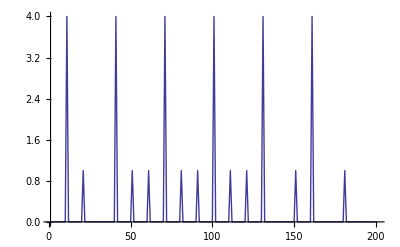

```mathematica
ΔfEOM=50;
ΔFSR=30;
```

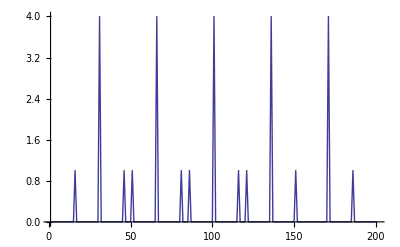

```mathematica
ΔfEOM=50;
ΔFSR=35;
```

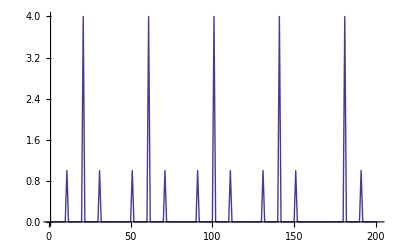

```mathematica
ΔfEOM=50;
ΔFSR=40;
```

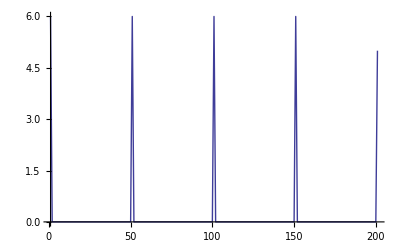

```mathematica
ΔfEOM=50;
ΔFSR=50;
```

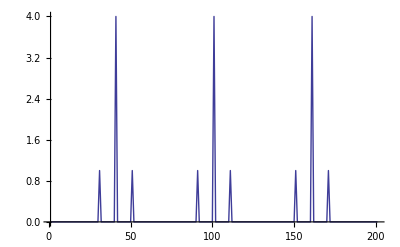

```mathematica
ΔfEOM=50;
ΔFSR=60;
```

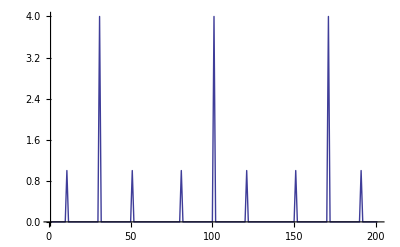

```mathematica
ΔfEOM=50;
ΔFSR=70;
```

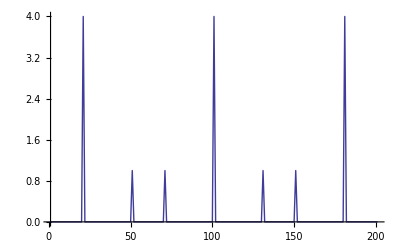

```mathematica
ΔfEOM=50;
ΔFSR=80;
```

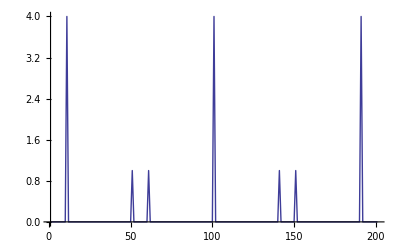

```mathematica
ΔfEOM=50;
ΔFSR=90;
```